```mathematica
Clear["Global`*"];
```

```mathematica
M=32;              
m=30000;         
ti=0.0;
tf=10500.0;          
h=(tf-ti)/m;     
modo=1;     
α=0.25;
```

```mathematica
(* CONDIÇÃO DE CONTORNO *)

Do [
{X[i,1]=Sin[modo*π *i/(M+1)],
P[i,1]=0},
{i,1,M}
];

X[0,_]:=0;
X[M+1,_]:=0;
```

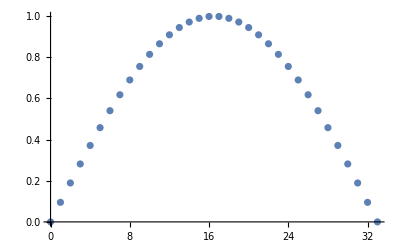

```mathematica
ListPlot[Table[{i,X[i,1]},{i,0,M+1}]]
```

```mathematica
Do[
(*k1,l1*)
Do[
k1[i]=h*P[i,n];
l1[i]=h*((X[i+1,n]+X[i-1,n]-2 X[i,n])+α*((X[i+1,n]-X[i,n])^2-(X[i,n]-X[i-1,n])^2));
,{i,1,M}];

(*X2,P2*)
Do[
X2[i]=X[i,n]+k1[i]/2;
P2[i]=P[i,n]+l1[i]/2;
,{i,1,M}];
X2[0]=0;X2[M+1]=0;

(*k2,l2*)
Do[
k2[i]=h*P2[i];
l2[i]=h*((X2[i+1]+X2[i-1]-2 X2[i])+α*((X2[i+1]-X2[i])^2-(X2[i]-X2[i-1])^2));
,{i,1,M}];

(*X3,P3*)
Do[
X3[i]=X[i,n]+k2[i]/2;
P3[i]=P[i,n]+l2[i]/2;
,{i,1,M}];
X3[0]=0;X3[M+1]=0;

(*k3,l3*)
Do[
k3[i]=h*P3[i];
l3[i]=h*((X3[i+1]+X3[i-1]-2 X3[i])+α*((X3[i+1]-X3[i])^2-(X3[i]-X3[i-1])^2));
,{i,1,M}];

(*X4,P4*)
Do[
X4[i]=X[i,n]+k3[i];
P4[i]=P[i,n]+l3[i];
,{i,1,M}];
X4[0]=0;X4[M+1]=0;

(*k4,l4*)
Do[
k4[i]=h*P4[i];
l4[i]=h*((X4[i+1]+X4[i-1]-2 X4[i])+α*((X4[i+1]-X4[i])^2-(X4[i]-X4[i-1])^2));
,{i,1,M}];

(*atualização temporal*)
Do[
X[i,n+1]=X[i,n]+(k1[i]+2 k2[i]+2 k3[i]+k4[i])/6;
P[i,n+1]=P[i,n]+(l1[i]+2 l2[i]+2 l3[i]+l4[i])/6;,{i,1,M}];
,{n,1,m}];
```

```mathematica
T[n_]:=Sum[1/2 P[i,n]^2,{i,1,M}];
V[n_]:=Sum[1/2 (X[i+1,n]-X[i,n])^2+α/3(X[i+1,n-X[i,n]]),{i,0,M}];
energia[n_]:=T[n]+V[n];
```

```mathematica
omega[s_]:=2 Sin[s Pi/(2 (M+1))];
Q[s_,n_]:=Sqrt[2./(M+1)]*Sum[X[j,n]*Sin[j s Pi/(M+1)],{j,1,M}];
Pmodo[s_,n_]:=Sqrt[2./(M+1)]*Sum[P[j,n]*Sin[j s Pi/(M+1)],{j,1,M}];
Eng[s_,n_]:=1/2 (Pmodo[s,n]^2+omega[s]^2 Q[s,n]^2);
```

```mathematica
energiasModos=Table[Table[Eng[s,n],{n,1,m}],{s,1,5}];
```

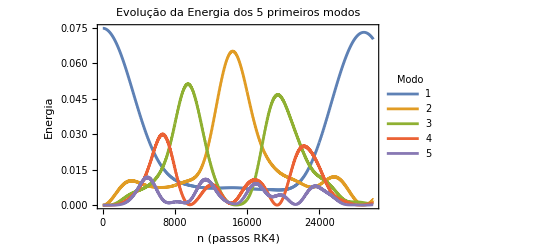

```mathematica
ListLinePlot[energiasModos,PlotRange->All,PlotLegends->LineLegend[Range[1,5],LegendLabel->"Modo"],Frame->True,FrameLabel->{"n (passos RK4)","Energia"},PlotLabel->"Evolução da Energia dos 5 primeiros modos"]
```

```mathematica
temposPlot={1000,10000,12000,14000,19000,22000,28311};
curvas=Table[Table[X[i,t],{i,1,M}],{t,temposPlot}];

labels=ToString/@temposPlot;
```

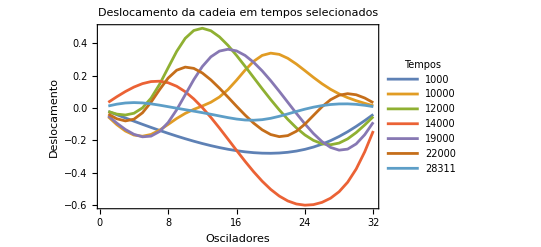

```mathematica
ListLinePlot[curvas,PlotRange->All,Frame->True,FrameLabel->{"Osciladores","Deslocamento"},PlotLegends->Placed[LineLegend[labels,LegendLabel->"Tempos"],Right],PlotLabel->"Deslocamento da cadeia em tempos selecionados"]
```

```mathematica
(* Gives full animation but it is to heavy for git*)
(*frames=Table[ListPlot[Table[X[i,n],{i,1,M}],PlotRange->{{1,M},{-1.2,1.2}},PlotLabel->"Oscilação da Cadeia Anarmônica"],{n,1,m,10}];

ListAnimate[frames]*)
```

```mathematica
(*Export["anh.gif",%]*)
```

```mathematica
frames=Table[Rasterize[ListPlot[Table[X[i,n],{i,1,M}],PlotRange->{{1,M},{-1.2,1.2}},PlotLabel->"Oscilação da Cadeia Anarmônica"],ImageResolution->72 (*Mantém a qualidade básica para tela*)],{n,1,m,10}];

ListAnimate[frames]
```